```mathematica
w
```

121 °

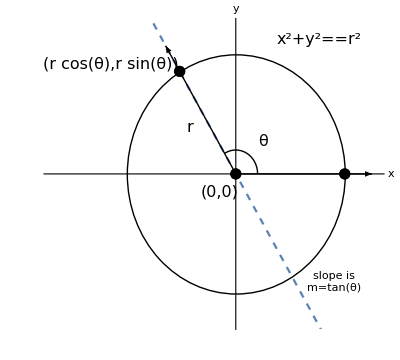

{trig-function-circle.pdf,trig-function-circle.svg}

```mathematica
r=4;
θ=121*Degree
Show[
Plot[{Tan[θ]x},{x,-5,5},PlotStyle->Dashed],
ListPlot[{{r Cos[θ],r Sin[θ]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{r ,0}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{0,0}},PlotStyle->{Black,PointSize[0.02]}],
Graphics[{Text[Style[HoldForm[r],16,Italic],{(r+1) Cos[θ]/2-0.4,(r+1) Sin[θ]/2-0.6}]}],
Graphics[{Text[Style["(r cos(θ),r sin(θ))",16,Italic],{(r+1) Cos[θ]-2,(r+1) Sin[θ]-0.6}]}],
Graphics[{Text[Style[HoldForm[x^2+y^2==r^2],16,Italic],{(r+1) Cos[θ/2]+0.6,(r+1) Sin[θ]+0.2}]}],
Graphics[{Text[Style["(0,0)",16,Italic],{0-0.6,0-0.6}]}],
Graphics[{Arrow[{{0,0},{(r+1) Cos[θ],(r+1) Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{(r+1) ,0}}]}],
Graphics[{Circle[{0,0},r]}],
Graphics[{Circle[{0,0},0.2r,{0,θ}]}],
Graphics[{Text[Style[HoldForm[θ],16],{0.2(r+1) Cos[θ/2]+0.5,0.2(r+1) Sin[θ/2]+0.2}]}],
Ticks->None,GridLines->None,
PlotRange->{{-(r+1)-2,r+1}+0.2,{-(r+1),r+1}},GridLines->Automatic,AspectRatio->0.9,AxesLabel->{"x","y"},AxesStyle->Directive[18],
Epilog->{Style[Text["slope is\nm=tan(θ)",{3.6,-3.6}],16]}]
Export[{"trig-function-circle.pdf","trig-function-circle.svg"},%]
```

207 °

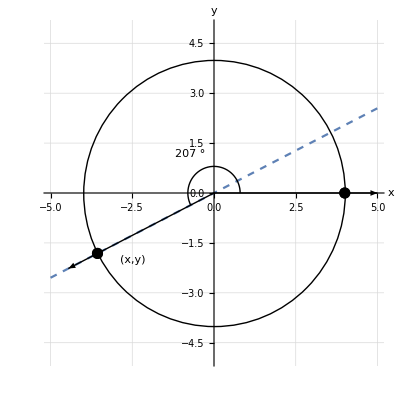

{circle207.pdf,circle207.svg}

```mathematica
r=4;
θ=207*Degree
Show[
Plot[{Tan[θ]x},{x,-5,5},PlotStyle->Dashed],
ListPlot[{{r Cos[θ],r Sin[θ]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{r ,0}},PlotStyle->{Black,PointSize[0.02]}],
Graphics[{Text[Style["(x,y)",Large,Italic],{-2.5,-2}]}],
Graphics[{Arrow[{{0,0},{(r+1) Cos[θ],(r+1) Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{(r+1) ,0}}]}],
Graphics[{Circle[{0,0},r]}],
Graphics[{Circle[{0,0},0.2r,{0,θ}]}],
Graphics[{Text[Style[θ,Large],{0.2(r+1) Cos[θ/2]-0.5,0.2(r+1) Sin[θ/2]+0.2}]}],

PlotRange->{{-(r+1),r+1},{-(r+1),r+1}},GridLines->Automatic,AspectRatio->1,AxesLabel->{"x","y"},AxesStyle->Directive[18]]
Export[{"circle207.pdf","circle207.svg"},%]
```

121 °

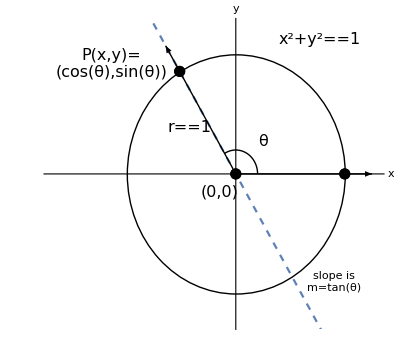

{trig-function-unit-circle.pdf,trig-function-unit-circle.svg}

```mathematica
r=4;
θ=121*Degree
Show[
Plot[{Tan[θ]x},{x,-5,5},PlotStyle->Dashed],
ListPlot[{{r Cos[θ],r Sin[θ]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{r ,0}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{0,0}},PlotStyle->{Black,PointSize[0.02]}],
Graphics[{Text[Style[HoldForm[r==1],16,Italic],{(r+1) Cos[θ]/2-0.4,(r+1) Sin[θ]/2-0.6}]}],
Graphics[{Text[Style["P(x,y)=\n(cos(θ),sin(θ))",16,Italic],{(r+1) Cos[θ]-2,(r+1) Sin[θ]-0.6}]}],
Graphics[{Text[Style[HoldForm[x^2+y^2==1],16,Italic],{(r+1) Cos[θ/2]+0.6,(r+1) Sin[θ]+0.2}]}],
Graphics[{Text[Style["(0,0)",16,Italic],{0-0.6,0-0.6}]}],
Graphics[{Arrow[{{0,0},{(r+1) Cos[θ],(r+1) Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{(r+1) ,0}}]}],
Graphics[{Circle[{0,0},r]}],
Graphics[{Circle[{0,0},0.2r,{0,θ}]}],
Graphics[{Text[Style[HoldForm[θ],16],{0.2(r+1) Cos[θ/2]+0.5,0.2(r+1) Sin[θ/2]+0.2}]}],
Ticks->None,GridLines->None,
PlotRange->{{-(r+1)-2,r+1}+0.2,{-(r+1),r+1}},GridLines->Automatic,AspectRatio->0.9,AxesLabel->{"x","y"},AxesStyle->Directive[18],
Epilog->{Style[Text["slope is\nm=tan(θ)",{3.6,-3.6}],16]}]
Export[{"trig-function-unit-circle.pdf","trig-function-unit-circle.svg"},%]
```